```mathematica
g=Table[Log[10,QuantityMagnitude[IsotopeData[{z,z+n},"Lifetime"]]],{z,0,118},{n,0,176}];
```

IsotopeData::notent: {0, 0} is not a known entity, class, or tag for IsotopeData. Use IsotopeData[] for a list of entities.

IsotopeData::notent: {0, 2} is not a known entity, class, or tag for IsotopeData. Use IsotopeData[] for a list of entities.

IsotopeData::notent: {0, 3} is not a known entity, class, or tag for IsotopeData. Use IsotopeData[] for a list of entities.

General::stop: Further output of IsotopeData::notent will be suppressed during this calculation.

```mathematica
g1=g//.{Log[QuantityMagnitude[_]]/Log[10]->0};
```

```mathematica
g2=Table[If[(0<Floor[x+y/2]<120)&&(0<Floor[x-y/2+1/4]<178),g1[[Floor[x+y/2],Floor[x-y/2+1/4]]],0],{y,-62,9,1/2},{x,1,148,1/2}];
```

```mathematica
Dimensions[g1]
```

{119,177}

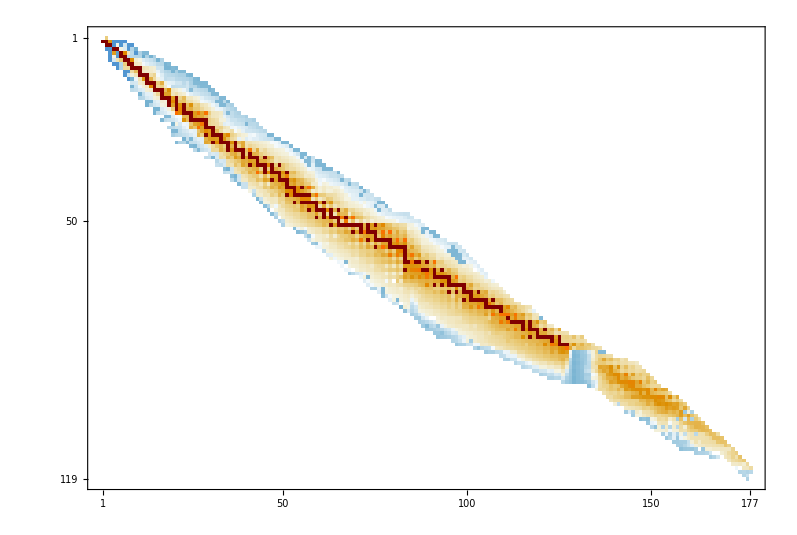

```mathematica
g1//MatrixPlot
```

```mathematica
g1[[50,60]]
```

3.7

```mathematica
Min[
```

```mathematica
g3 = Table[If[0≤x+y≤118&&0≤x+2*y≤176,g1[[1+x+y,1+x+2*y]],0],{x,-4,69},{y,-8,61}];
```

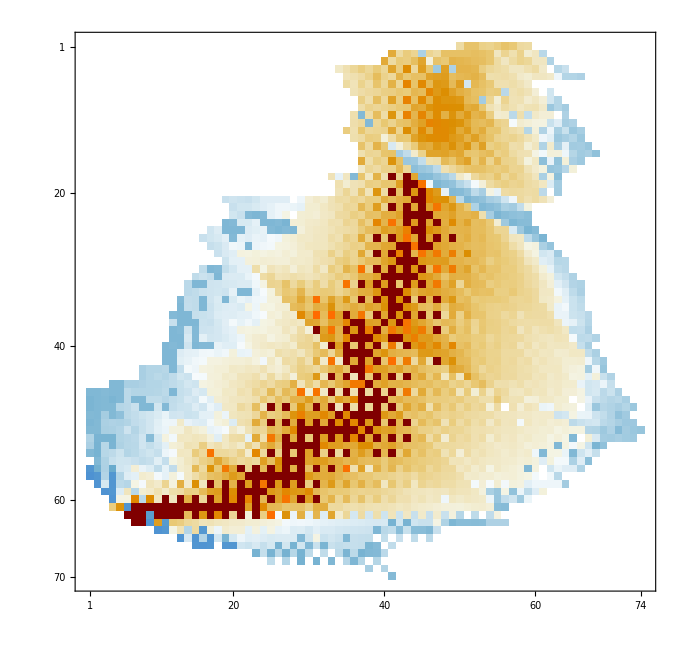

```mathematica
Reverse@Transpose[g3]//MatrixPlot
```

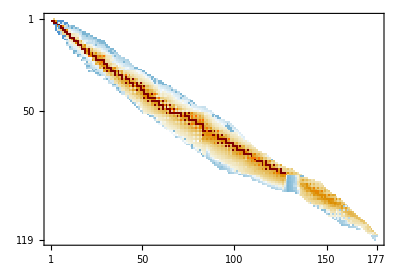

```mathematica
g1//MatrixPlot
```

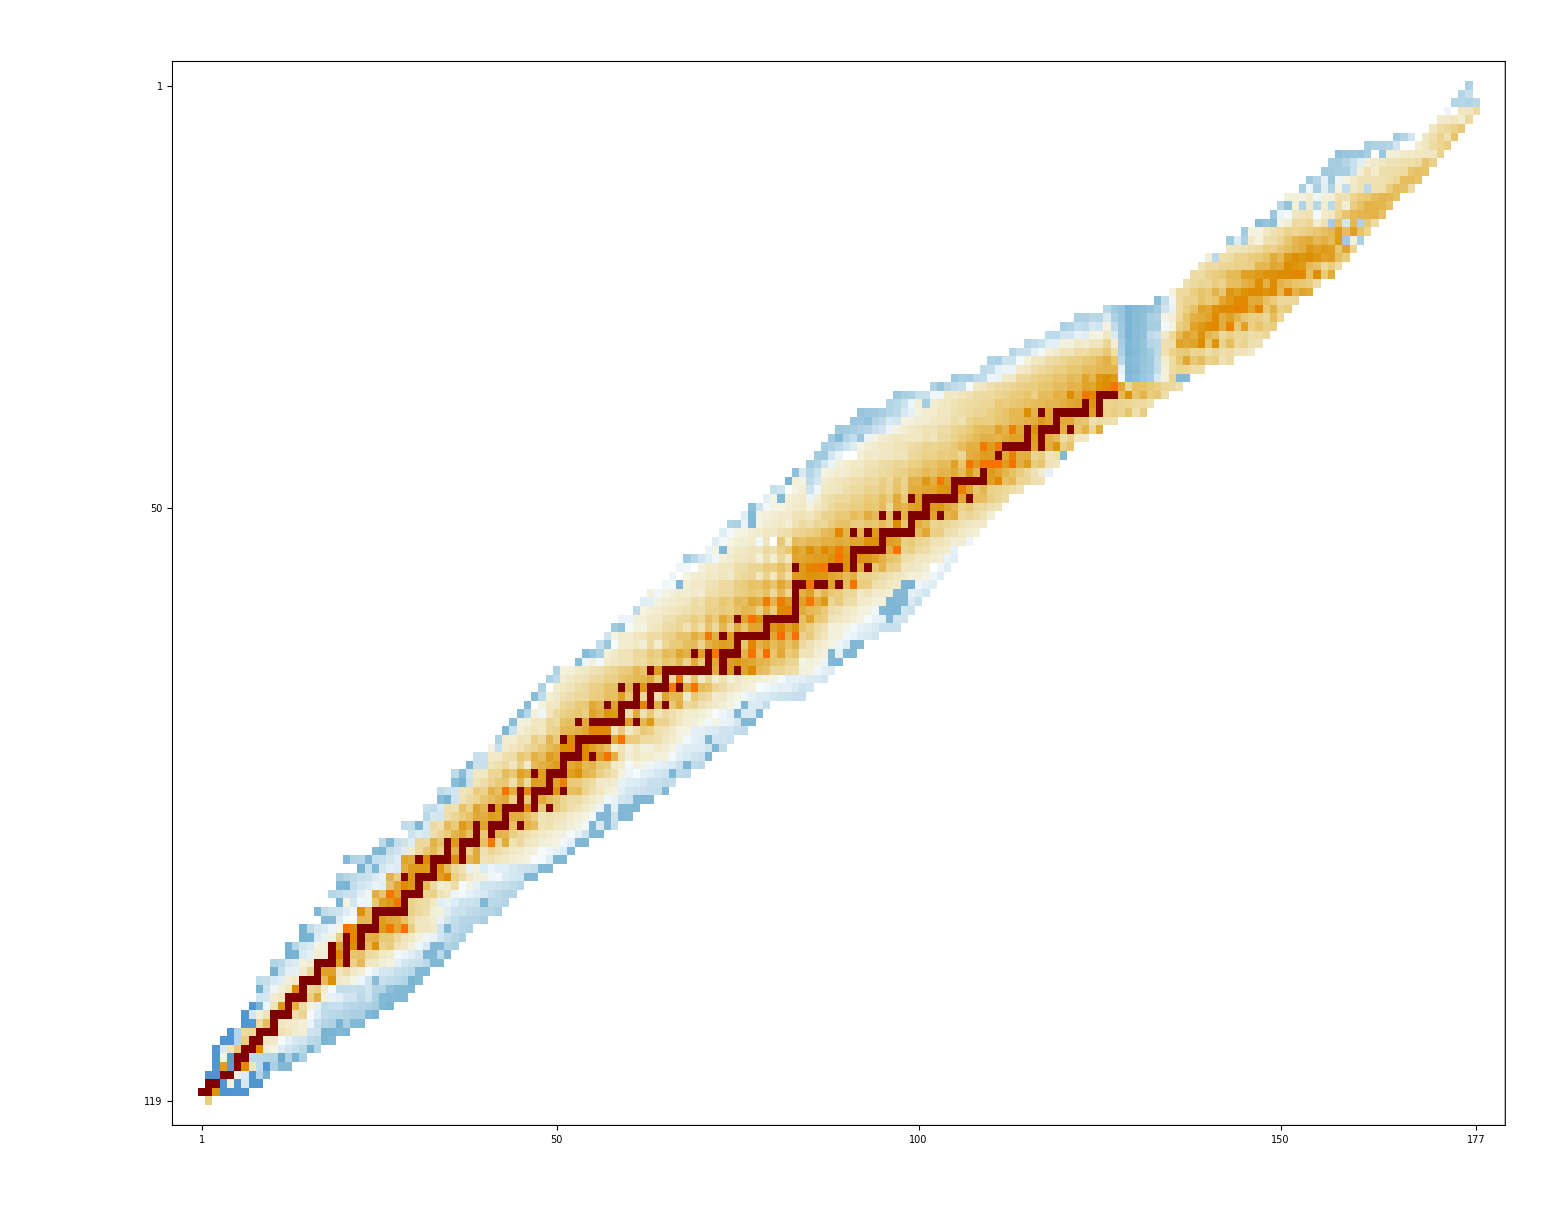

```mathematica
MatrixPlot[Reverse@g1,ImagePadding->20,ImageSize->(10*Reverse[Dimensions[g1]]+2*20)]
```

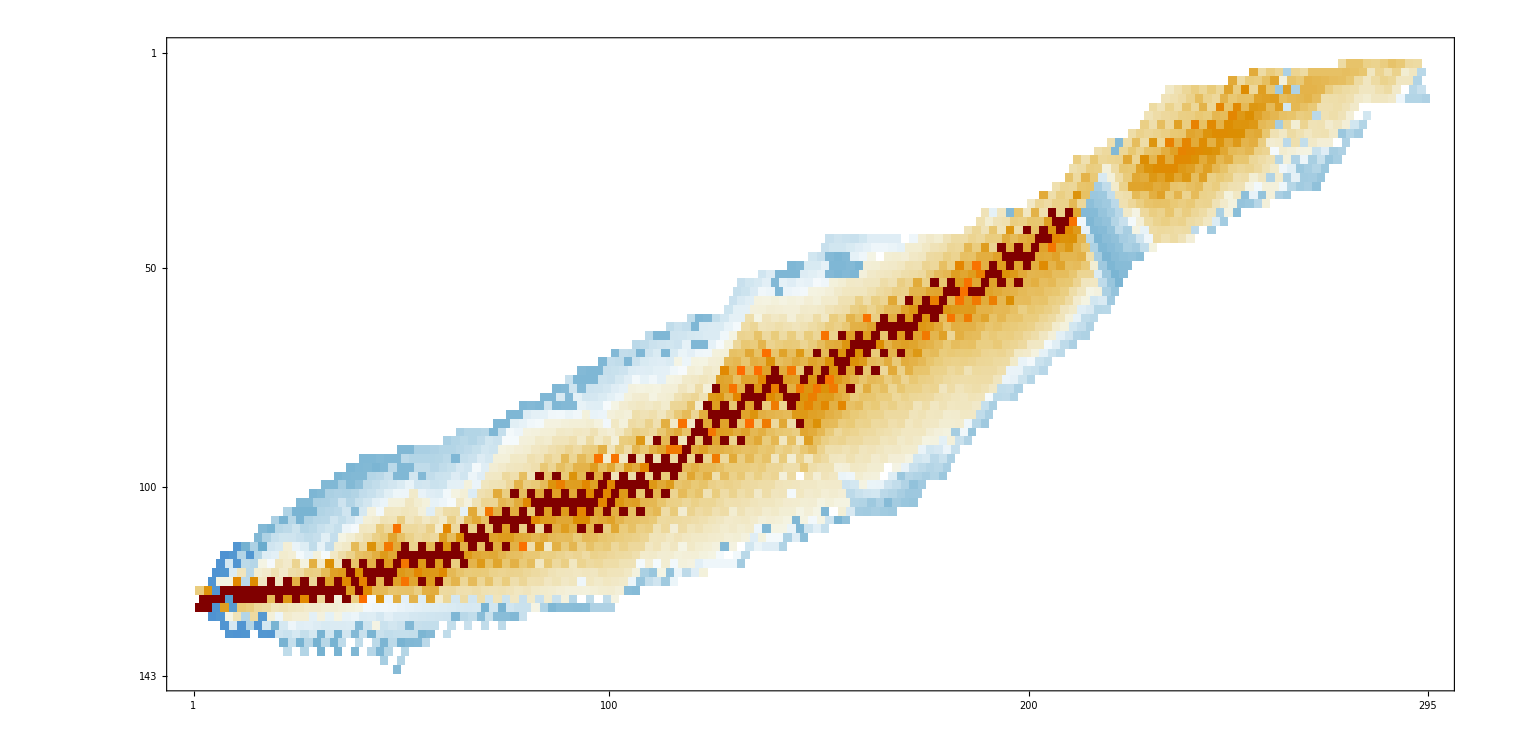

```mathematica
MatrixPlot[g2,ImagePadding->20,ImageSize->(5*Reverse[Dimensions[g2]]+2*20)]
```

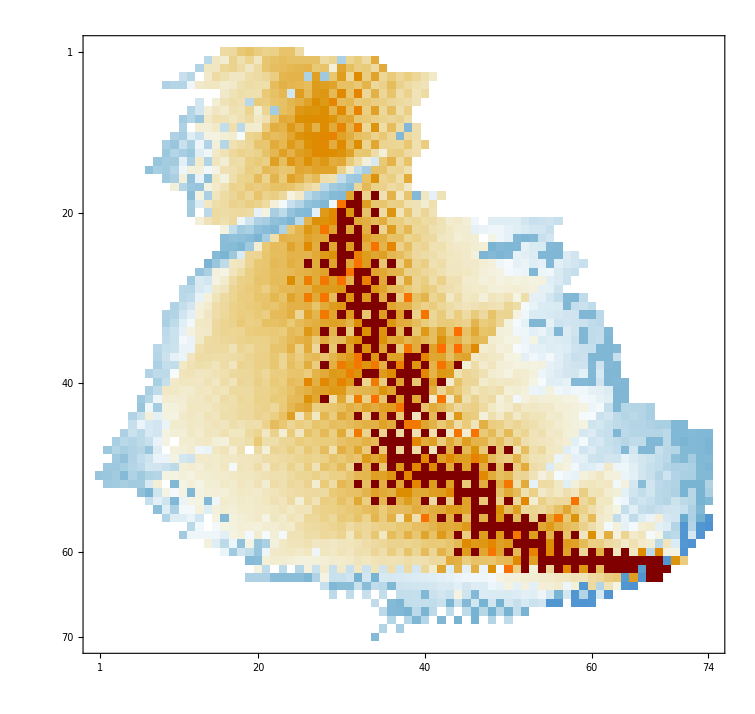

```mathematica
Reverse@Transpose[Reverse@g3]//MatrixPlot
```

```mathematica
g=Table[Log[10,QuantityMagnitude[IsotopeData[{z,z+n},"Lifetime"]]],{z,0,118},{n,0,176}];
```

```mathematica
g
```

{{Log[QuantityMagnitude[IsotopeData[{0,0},Lifetime]]]/Log[10],2.947,Log[QuantityMagnitude[IsotopeData[{0,2},Lifetime]]]/Log[10],Log[QuantityMagnitude[IsotopeData[{0,3},Lifetime]]]/Log[10],Log[QuantityMagnitude[IsotopeData[{0,4},Lifetime]]]/Log[10],167,Log[QuantityMagnitude[IsotopeData[{0,172},Lifetime]]]/Log[10],Log[QuantityMagnitude[IsotopeData[{0,173},Lifetime]]]/Log[10],Log[QuantityMagnitude[IsotopeData[{0,174},Lifetime]]]/Log[10],Log[QuantityMagnitude[IsotopeData[{0,175},Lifetime]]]/Log[10],Log[QuantityMagnitude[IsotopeData[{0,176},Lifetime]]]/Log[10]},117,{Log[QuantityMagnitude[1]]/Log[10],175,Log[1]/Log[10]}}
 |  |  |  |

```mathematica
IsotopeData[{30,30+40},"Lifetime"]
```

5.9×10^23 s

```mathematica
is = IsotopeData[]
```

{Entity[Isotope,Neutron],hydrogen-1,deuterium,tritium,hydrogen-4,hydrogen-5,hydrogen-6,hydrogen-7,helium-2,helium-3,helium-4,helium-5,helium-6,helium-7,helium-8,helium-9,helium-10,lithium-3,lithium-4,lithium-5,lithium-6,lithium-7,lithium-8,lithium-9,lithium-10,lithium-11,lithium-12,beryllium-5,beryllium-6,beryllium-7,beryllium-8,beryllium-9,beryllium-10,beryllium-11,beryllium-12,beryllium-13,beryllium-14,beryllium-15,beryllium-16,boron-6,boron-7,boron-8,boron-9,boron-10,boron-11,boron-12,boron-13,boron-14,boron-15,boron-16,boron-17,boron-18,boron-19,carbon-8,carbon-9,carbon-10,carbon-11,carbon-12,carbon-13,carbon-14,carbon-15,carbon-16,carbon-17,carbon-18,carbon-19,carbon-20,carbon-21,carbon-22,nitrogen-10,nitrogen-11,nitrogen-12,nitrogen-13,nitrogen-14,nitrogen-15,nitrogen-16,nitrogen-17,nitrogen-18,nitrogen-19,nitrogen-20,nitrogen-21,nitrogen-22,nitrogen-23,nitrogen-24,nitrogen-25,oxygen-12,oxygen-13,oxygen-14,oxygen-15,oxygen-16,oxygen-17,oxygen-18,oxygen-19,oxygen-20,oxygen-21,oxygen-22,oxygen-23,oxygen-24,oxygen-25,oxygen-26,oxygen-27,2984,bohrium-266,bohrium-267,bohrium-268,bohrium-269,bohrium-270,bohrium-271,bohrium-272,bohrium-273,bohrium-274,bohrium-275,hassium-263,hassium-264,hassium-265,hassium-266,hassium-267,hassium-268,hassium-269,hassium-270,hassium-271,hassium-272,hassium-273,hassium-274,hassium-275,hassium-276,hassium-277,meitnerium-265,meitnerium-266,meitnerium-267,meitnerium-268,meitnerium-269,meitnerium-270,meitnerium-271,meitnerium-272,meitnerium-273,meitnerium-274,meitnerium-275,meitnerium-276,meitnerium-277,meitnerium-278,meitnerium-279,darmstadtium-267,darmstadtium-268,darmstadtium-269,darmstadtium-270,darmstadtium-271,darmstadtium-272,darmstadtium-273,darmstadtium-274,darmstadtium-275,darmstadtium-276,darmstadtium-277,darmstadtium-278,darmstadtium-279,darmstadtium-280,darmstadtium-281,roentgenium-272,roentgenium-273,roentgenium-274,roentgenium-275,roentgenium-276,roentgenium-277,roentgenium-278,roentgenium-279,roentgenium-280,roentgenium-281,roentgenium-282,roentgenium-283,copernicium-277,copernicium-278,copernicium-279,copernicium-280,copernicium-281,copernicium-282,copernicium-283,copernicium-284,copernicium-285,Entity[Isotope,Ununtrium283],Entity[Isotope,Ununtrium284],Entity[Isotope,Ununtrium285],Entity[Isotope,Ununtrium286],Entity[Isotope,Ununtrium287],flerovium-285,flerovium-286,flerovium-287,flerovium-288,flerovium-289,Entity[Isotope,Ununpentium287],Entity[Isotope,Ununpentium288],Entity[Isotope,Ununpentium289],Entity[Isotope,Ununpentium290],Entity[Isotope,Ununpentium291],livermorium-289,livermorium-290,livermorium-291,livermorium-292,Entity[Isotope,Ununseptium291],Entity[Isotope,Ununseptium292],Entity[Isotope,Ununseptium293],Entity[Isotope,Ununseptium294],Entity[Isotope,Ununoctium293]}
 |  |  |  |

```mathematica
is[[-1]]
```

Entity[Isotope,Ununoctium293]

```mathematica
IsotopeData[0]
```

IsotopeData::notent: 0 is not a known entity, class, or tag for IsotopeData. Use IsotopeData[] for a list of entities.

IsotopeData[0]

```mathematica
IsotopeData[#,"NeutronNumber"]&/@Range[0,118]
```

IsotopeData::notent: 0 is not a known entity, class, or tag for IsotopeData. Use IsotopeData[] for a list of entities.

{IsotopeData[0,NeutronNumber],{0,1,2,3,4,5,6},{0,1,2,3,4,5,6,7,8},{0,1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22},{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24},{7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26},{7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28},{8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29},{8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30},{9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31},{10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33},{11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34},{12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35},{13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36},{14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37},{15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39},{16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41},{17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42},{18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43},{19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44},{19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46},{20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48},{20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50},{23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51},{24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53},{25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55},{26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57},{27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59},{31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60},{32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62},{33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64},{34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65},{35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67},{37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69},{38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70},{40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72},{41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73},{42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75},{43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76},{44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77},{45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78},{46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83},{47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84},{48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86},{49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87},{52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88},{53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90},{55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91},{56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93},{57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96},{58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97},{60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98},{61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99},{62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101},{65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102},{66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103},{67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104},{70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105},{71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106},{72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107},{73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108},{75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109},{76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110},{78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112},{79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113},{81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116},{82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117},{84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118},{85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119},{86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120},{87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122},{88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124},{90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126},{91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130},{95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131},{96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133},{101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136},{104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136},{108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138},{109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142},{112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145},{114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146},{117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147},{119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148},{121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149},{125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150},{132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151},{134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153},{136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154},{137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156},{138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157},{139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158},{141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159},{142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160},{144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161},{146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162},{148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163},{149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164},{150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165},{152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167},{153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168},{155,156,157,158,159,160,161,162,163,164,165,166,167,168,169},{156,157,158,159,160,161,162,163,164,165,166,167,168,169,170},{157,158,159,160,161,162,163,164,165,166,167,168,169,170,171},{161,162,163,164,165,166,167,168,169,170,171,172},{165,166,167,168,169,170,171,172,173},{170,171,172,173,174},{171,172,173,174,175},{172,173,174,175,176},{173,174,175,176},{174,175,176,177},{175}}